## First Look at Lists

Lists are a basic way to collect things together in the Wolfram Language. {1,2,3} is a list of numbers. On their own, lists don’t do anything; they’re just a way to store things. So if you give a list as input, it’ll just come back unchanged:

```mathematica
{1,2,3,4,a,b,c}
```

{1,2,3,4,a,b,c}

ListPlot is a function that makes a plot of a list of numbers.

Plot the list of numbers {1,1,2,2,3,4,4}:

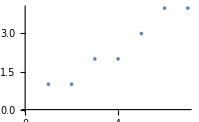

```mathematica
ListPlot[{1,1,2,2,3,4,4}]
```

Plot the list of numbers {10,9,8,7,3,2,1}:

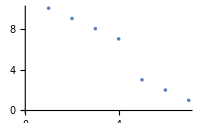

```mathematica
ListPlot[{10,9,8,7,3,2,1}]
```

Range is a function that makes a list of numbers.

Generate a list of numbers up to 10:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Generate a list of numbers, then plot it:

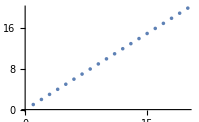

```mathematica
ListPlot[Range[20]]
```

Reverse reverses the elements in a list.

Reverse the elements in a list:

```mathematica
Reverse[{1,2,3,4}]
```

{4,3,2,1}

Reverse what Range has generated:

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

Plot the reversed list:

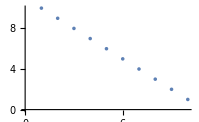

```mathematica
ListPlot[Reverse[Range[10]]]
```

Join joins lists together, making a single list as the result.

Join lists together:

```mathematica
Join[{1,2,3},{4,5},{6,7}]
```

{1,2,3,4,5,6,7}

```mathematica
Join[{1,2,3},{1,2,3,4,5}]
```

{1,2,3,1,2,3,4,5}

Join two lists made by Range:

```mathematica
Join[Range[3],Range[5]]
```

{1,2,3,1,2,3,4,5}

Plot three lists joined together:

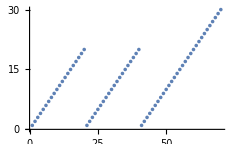

```mathematica
ListPlot[Join[Range[20],Range[20],Range[30]]]
```

Reverse the list in the middle:

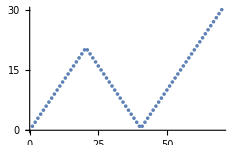

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]],Range[30]]]
```

Vocabulary

{1,2,3,4} |   | list of elements 
ListPlot[{1,2,3,4}] |   | plot a list of numbers 
Range[10] |   | range of numbers 
Reverse[{1,2,3}] |   | reverse a list 
Join[{4,5,6},{2,3,2}] |   | join lists together

"11 Exercises Available"
"with 5 extras" | "Get Started »"

Use Range to create the list {1,2,3,4}. »

| Expected output: |  
  | {1,2,3,4} |

Make a list of numbers up to 100. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

Use Range and Reverse to create {4,3,2,1}. »

| Expected output: |  
  | {4,3,2,1} |

Make a list of numbers from 1 to 50 in reverse order. »

| Expected output: |  
  | {50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1} |

Use Range, Reverse and Join to create {1,2,3,4,4,3,2,1}. »

| Expected output: |  
  | {1,2,3,4,4,3,2,1} |

Plot a list that counts up from 1 to 100, then down to 1. »

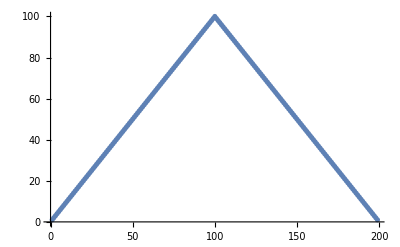
| Expected output: |  
  | -Graphics- |

Use Range and RandomInteger to make a list with a random length up to 10. »

| Sample expected output: |  
  | {1} |

Find a simpler form for Reverse[Reverse[Range[10]]]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10} |

Find a simpler form for Join[{1,2},Join[{3,4},{5}]]. »

| Expected output: |  
  | {1,2,3,4,5} |

Find a simpler form for Join[Range[10],Join[Range[10],Range[5]]]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5} |

Find a simpler form for Reverse[Join[Range[20],Reverse[Range[20]]]]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1} |

Compute the reverse of the reverse of {1,2,3,4}. »

| Expected output: |  
  | {1,2,3,4} |

Use Range, Reverse and Join to create the list {1,2,3,4,5,4,3,2,1}. »

| Expected output: |  
  | {1,2,3,4,5,4,3,2,1} |

Use Range, Reverse and Join to create {3,2,1,4,3,2,1,5,4,3,2,1}. »

| Expected output: |  
  | {3,2,1,4,3,2,1,5,4,3,2,1} |

Plot the list of numbers {10,11,12,13,14}. »

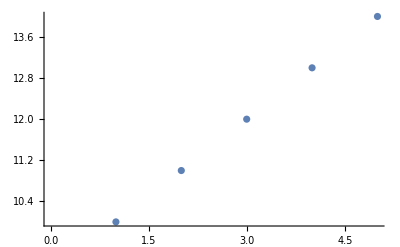
| Expected output: |  
  | -Graphics- |

Find a simpler form for Join[Join[Range[10],Reverse[Range[10]]],Range[10]]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,10,9,8,7,6,5,4,3,2,1,1,2,3,4,5,6,7,8,9,10} |

Q&A

How does one read {1,2,3} out loud?

Usually “list 1 2 3”. “{” and “}” are called “braces” or “curly brackets”. “{” is “open brace” and “}” is “close brace”.

Is a list a function?

Yes. {1,2,3} is List[1,2,3]. But unlike, say, Plus, the function List doesn’t actually compute anything; it just comes back unchanged.

What is ListPlot plotting?

The values of successive list elements. The x value of each point gives the position in the list; the y value gives the value of that element.

How long can lists be?

As long as you want, until your computer runs out of memory.

Tech Notes

Range[m,n] generates numbers from m to n. Range[m,n,s] generates numbers from m to n in steps of s.

Many computer languages have constructs like lists (often called “arrays”). But usually they only allow lists of explicit things, like numbers; you can’t have a list like {a,b,c} where you haven’t said what a, b and c are. You can in the Wolfram Language, though, because the Wolfram Language is symbolic.

{a,b,c} is a list of elements in a definite order; {b,c,a} is a different list.

Like in math, you can make theorems about Wolfram Language functions. For example, Reverse[Reverse[x]] is equal to x.

More to Explore

Guide to Lists in the Wolfram Language »